## NF theory for 2d domain with 3-component Turing equations

```mathematica
T=700;
δ=10;
```

```mathematica
eval=Thread[{kba,kbc,kcb,kab,kac,μ,β,v1,v2,v3,da,db,n}->{3.,3.,3.,100,100,0.0076,0.09,70,100,40,1,0.0015,2}];
```

```mathematica
ha[m_,k_]:=m^n/(m^n+k^n)
hi[m_,k_]:=k^n/(m^n+k^n)
```

```mathematica
f[a_,b_,c_]:=v1 (*ha[a,kaa]*)hi[b,kba]-μ a+β
g[a_,b_,c_]:=v2 ha[a,kab]hi[c,kcb]-μ b+β
h[a_,b_,c_]:=v3 hi[a,kac]hi[b,kbc](*ha[c,kcc]*)-μ c+β
```

```mathematica
fp=Flatten[NSolve[{f[a0,b0,c0],g[a0,b0,c0],h[a0,b0,c0]}/.eval,{a0,b0,c0},Reals]]
```

{b0→41.7803,c0→31.8528,a0→59.0866}

```mathematica
zeros=Thread[{a,b,c}->ConstantArray[0,3]];
```

```mathematica
j=D[{f[a+a0,b+b0,c+c0],g[a+a0,b+b0,c+c0],h[a+a0,b+b0,c+c0]},{{a,b,c}}]/.eval/.fp/.zeros;
jd=j-k^2DiagonalMatrix[{da,db,0}];
```

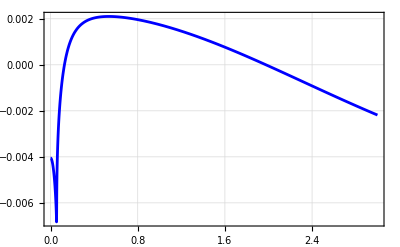

```mathematica
Plot[Max[Re[Eigenvalues[jd]/.eval]],{k,0,3},PlotRange->All,Frame->True,GridLines->Automatic,PlotStyle->Blue]
```

#### Numerical solution on a 2d domain

```mathematica
Ω=DiscretizeRegion[Rectangle[{-L,-L},{L,L}],Method->"Continuation",AccuracyGoal->7,PrecisionGoal->7,MaxCellMeasure->{"Area"->0.2}];
```

```mathematica
L=2Pi;
T=100;
η=5;
```

```mathematica
eqn={1/δ D[a[t,x,y],{t,1}]==da( D[a[t,x,y],{x,2}]+D[a[t,x,y],{y,2}])+f[a[t,x,y],b[t,x,y],c[t,x,y]],1/δ D[b[t,x,y],{t,1}]==db (D[b[t,x,y],{x,2}]+D[b[t,x,y],{y,2}])+g[a[t,x,y],b[t,x,y],c[t,x,y]],1/δ D[c[t,x,y],{t,1}]==h[a[t,x,y],b[t,x,y],c[t,x,y]]}/.eval/.fp;
```

```mathematica
ic={a[0,x,y]==a0+0.01(Cos[x]+0.5Cos[2x])/.fp,b[0,x,y]==b0+0.01(Cos[x]+0Cos[2x])/.fp,c[0,x,y]==c0+0.01Cos[x]+0.Cos[2x]}/.fp;
```

```mathematica
pbc={PeriodicBoundaryCondition[a[t,x,y],x==-L,TranslationTransform[{2L,0}]],PeriodicBoundaryCondition[a[t,x,y],y==-L,TranslationTransform[{0,2L}]],PeriodicBoundaryCondition[b[t,x,y],x==-L,TranslationTransform[{2L,0}]],PeriodicBoundaryCondition[b[t,x,y],y==-L,TranslationTransform[{0,2L}]],PeriodicBoundaryCondition[c[t,x,y],x==-L,TranslationTransform[{2L,0}]],PeriodicBoundaryCondition[c[t,x,y],y==-L,TranslationTransform[{0,2L}]]};
```

```mathematica
T=1000;
```

```mathematica
{asol,bsol,csol}=NDSolveValue[{eqn,ic,pbc},{a,b,c},{t,0,T},Element[{x,y},Ω]];
```

```mathematica
frames=Table[DensityPlot[asol[t,x,y],{x,-L,L},{y,-L,L},PlotRange->(*{-0.1,0.2}*)All,Mesh->None,AspectRatio->True],{t,0,T,10}];
ListAnimate[frames]
```

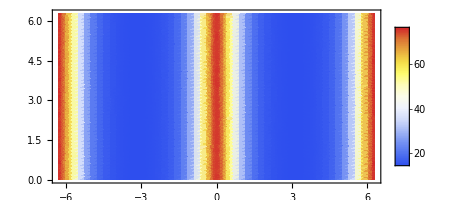

```mathematica
dp1=DensityPlot[csol[600,x,y],{x,-L,L},{y,0,L},PlotRange->All,Mesh->None,AspectRatio->True,BaseStyle->{FontFamily->"CMU Serif",20},PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotPoints->50]
```

#### Fitting the data along x axis with NF equation

```mathematica
data=Table[Table[1/Pi NIntegrate[Cos[k x]csol[t,x,0],{x,-Pi,Pi},PrecisionGoal->4,AccuracyGoal->5,Method->{Automatic,"SymbolicProcessing"->0}],{t,0,T,5}],{k,0,4}];
```

```mathematica
z=data[[2]];
times=Table[i,{i,Dimensions[z][[1]]}];
ztofit=Table[{times[[i]],-z[[i]]},{i,Dimensions[z][[1]]}];
```

```mathematica
rsol=DSolve[{r'[x]==p1 r[x]-p2 r[x]^3,r[0]==r0},r[x],x,Assumptions->{r0>0,p1>0,p2>0}]//Quiet//FullSimplify;
```

```mathematica
functofit=r[x]/.rsol[[1,1]]
```

(ⅇ^(p1 x) √p1 r0)/(√(p1-p2 r0^2) √(1+(ⅇ^(2 p1 x) p2 r0^2)/(p1-p2 r0^2)))

```mathematica
fit=NonlinearModelFit[ztofit,functofit,{{r0,0.01},{p1,0.4},{p2,0.0005}},x]
```

FittedModel[…]

```mathematica
param=fit["BestFitParameters"]
```

{r0→-0.000474547,p1→0.10459,p2→0.000195345}

```mathematica
p=Plot[-functofit/.param,{x,0,200},PlotStyle->{Thick,Red},BaseStyle->{FontFamily->"CMU Serif",14}];
simIn=ListLinePlot[Re[z],PlotStyle->{Thick,Blue},BaseStyle->{FontFamily->"CMU Serif",14}];
```

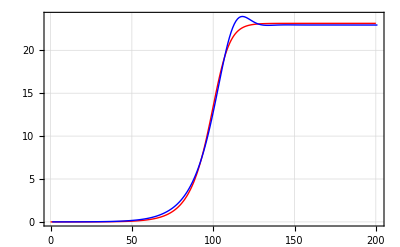

```mathematica
rdyn2d=Show[{p,simIn},PlotRange->All,Frame->True,GridLines->Automatic]
```

```mathematica
z1t=-functofit/.x->t/.param
```

(0.000474547 ⅇ^(0.10459 t))/(√(1+4.20603×10^-10 ⅇ^(0.20918 t)))

#### Solution is fit at 3 timepoints

```mathematica
{t1,t2,t3}={90,102,150};
```

```mathematica
k0[t_]:=1/(2Pi) NIntegrate[csol[5t,x,0],{x,-Pi,Pi}]
```

```mathematica
{k01,k02,k03}=k0[{t1,t2,t3}]
```

{31.8529,31.7695,29.4069}

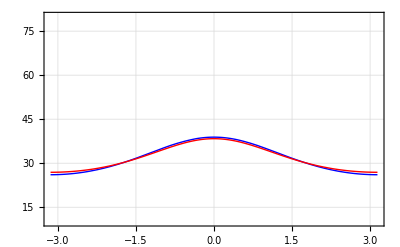

```mathematica
plt1=Plot[{csol[t,x,0]/.t->5t1,k01+z1t Cos[x]+0.0241z1t^2Cos[2x]+0.00049z1t^3Cos[3x]+0.000009z1t^4Cos[4x]/.t->t1/.fp},{x,-Pi,Pi},PlotRange->{10,80},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14}]
```

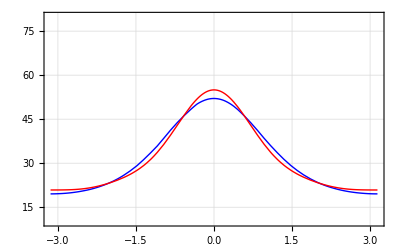

```mathematica
plt2=Plot[{csol[t,x,0]/.t->5t2,k02+z1t Cos[x]+0.0242z1t^2Cos[2x]+0.00049z1t^3Cos[3x]+0.000009z1t^4Cos[4x]/.t->t2/.fp},{x,-Pi,Pi},PlotRange->{10,80},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14}]
```

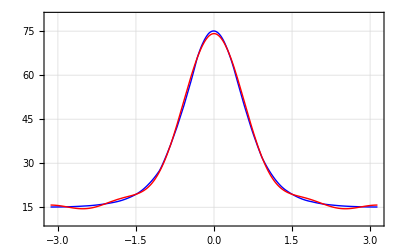

```mathematica
plt3=Plot[{csol[t,x,0]/.t->5t3,k03+z1t Cos[x]+0.0242z1t^2Cos[2x]+0.00049z1t^3Cos[3x]+0.000009z1t^4Cos[4x]/.t->t3/.fp},{x,-Pi,Pi},PlotRange->{10,80},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14}]
```

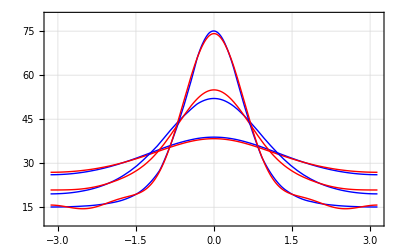

```mathematica
twodimfit=Show[plt1,plt2,plt3]
```